```mathematica
Exit[]
```

# Complete Markets

## An Example

There are two consumers Bruce (B) and Sheila (S), there are two time periods (t=0) and (t=1). Moreover, at t=1 there are two possible states (H) and (L).  The probability of state H is p and the probability of state L is 1-p. Bruce and Sheila maximize their respective expected discounted utility. In this economy, there is only one consumption good at each time-event pair (0, H, and L).

The following contingent goods are trade at period zero:

c0 ( a contract the promises one unit of consumption to be delivered at t=0).

cH ( a contract the promises one unit of consumption to be delivered at t=1 if and only if state H happens).

cL ( a contract the promises one unit of consumption to be delivered at t=1 if and only if state L happens).

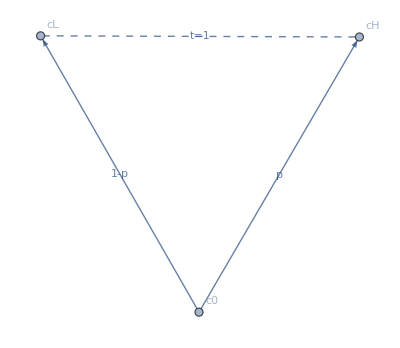

```mathematica
Graph[{Labeled[c0->cH,"p"],Labeled[c0->cL,"1-p"],Labeled[cH<->cL,"t=1"]},VertexLabels->"Name",EdgeStyle->{cH<->cL->Dashed}]
```

```mathematica
u[s][c_]:=Log[c] (* Sheila's utility for consumption *)
u[b][c_]:=Log[c] (* Bruce's utility for consumption *)
u[s][c]
u[b][c]
```

Log[c]

Log[c]

There is no production but consumers are endowed with contingent goods .

```mathematica
prices={p0,pH,pL}  (* price of contingent goods *)
basket={c0,cH,cL} (* basket of contingent goods *)
p0=1 (* always possible to normalize one of the prices to 1 *)
e[b]={10,1,1} (* endowment of Bruce *)
e[s]={1,10,10} (* endowment of Sheila *)
```

{p0,pH,pL}

{c0,cH,cL}

1

{10,1,1}

{1,10,10}

### Review Questions

Describe the basket (0,1,1).
Answer: The basket (0,1,1) is a contract that delivers one unit of consumption good in period t=1.

Describe the basket (1,0,1).
Answer: The basket (1,0,1) is a contract that delivers one unit of consumption good in period t=0 AND one unit of consumption in period t=1 if the state L happens. In particular the basket (1,0,1) delivers zero units of consumption in period t=1 when the state H happens.

Describe Bruce and Sheila’s incomes.
Answer: Their income is the value of their respective endowments.

```mathematica
prices.e[b]
prices.e[s]
```

10

10 pH+10 pL

Describe the total supply (of each contingent good) in this economy.
Answer: Since there is no production, the supply is just the sum of the consumers’ endowments. In particular, the supply of any contingent good is perfectly inelastic. In the current example the supply of is

```mathematica
e[b]+e[s] (* (supply of c0, supply of cH, supply of cL)*)
```

{10,10,10}

## Defining the Discounted Expected Utility

```mathematica
U[i]:=u[i][c0]+δ[i]*(p*u[i][cH]+(1-p)*u[i][cL])  (*the variable i indexes the consumer so i = b or s *)
```

δ[i] is the discount factor of consumer i: different consumers may have different discount rates!

```mathematica
U[i]
```

u[i][c0]+δ[i] (p u[i][cH]+(1-p) u[i][cL])

```mathematica
U[i]/.i->s
U[i]/.i->b
```

Log[c0]+(p Log[cH]+(1-p) Log[cL]) δ[s]

Log[c0]+(p Log[cH]+(1-p) Log[cL]) δ[b]

## Finding the Individual Demands

```mathematica
L=U[i]-λ*(prices.basket-income[i])
```

-λ (c0+cH pH+cL pL-income[i])+u[i][c0]+δ[i] (p u[i][cH]+(1-p) u[i][cL])

```mathematica
vars=Join[basket,{λ}]
grad=Grad[L,vars]
FOC=Thread[grad==0]
sysb=FOC/.i->b
BruceDemand=Solve[sysb,vars][[1]]
```

{c0,cH,cL,λ}

{-λ+u[i]'[c0],-pH λ+p δ[i] u[i]'[cH],-pL λ+(1-p) δ[i] u[i]'[cL],-c0-cH pH-cL pL+income[i]}

{-λ+u[i]'[c0]==0,-pH λ+p δ[i] u[i]'[cH]==0,-pL λ+(1-p) δ[i] u[i]'[cL]==0,-c0-cH pH-cL pL+income[i]==0}

{1/c0-λ==0,-pH λ+(p δ[b])/cH==0,-pL λ+((1-p) δ[b])/cL==0,-c0-cH pH-cL pL+income[b]==0}

{c0→income[b]/(1+δ[b]),cH→(p income[b] δ[b])/(pH (1+δ[b])),cL→(income[b] δ[b]-p income[b] δ[b])/(pL (1+δ[b])),λ→(1+δ[b])/income[b]}

```mathematica
syss=FOC/.i->s
SheilaDemand=Solve[syss,vars][[1]]
```

{1/c0-λ==0,-pH λ+(p δ[s])/cH==0,-pL λ+((1-p) δ[s])/cL==0,-c0-cH pH-cL pL+income[s]==0}

{c0→income[s]/(1+δ[s]),cH→(p income[s] δ[s])/(pH (1+δ[s])),cL→(income[s] δ[s]-p income[s] δ[s])/(pL (1+δ[s])),λ→(1+δ[s])/income[s]}

## Finding equilibrium prices

#### Market Clearing conditions

Endowments:

```mathematica
e[b]
e[s]
```

{10,1,1}

{1,10,10}

```mathematica
e[b]+e[s] (* mkt supply, inelastic!*)
```

{11,11,11}

```mathematica
mktclear={(c0/.BruceDemand)+(c0/.SheilaDemand)==e[b][[1]]+e[s][[1]],(cH/.BruceDemand)+(cH/.SheilaDemand)==e[b][[2]]+e[s][[2]]} (* Demand of c0 == Supply of c0, Demand of cH == Supply of cH, you can pick any two markets since we are solving for two prices. pH and pL.*)
```

{income[b]/(1+δ[b])+income[s]/(1+δ[s])==11,(p income[b] δ[b])/(pH (1+δ[b]))+(p income[s] δ[s])/(pH (1+δ[s]))==11}

Remember the incomes are now endogenous. They are the value of endowments (endowment quantities times respective prices) and prices are now endogenous.

```mathematica
MKTClear=mktclear/.{income[b]->prices.e[b],income[s]->prices.e[s]}
```

{(10+pH+pL)/(1+δ[b])+(1+10 pH+10 pL)/(1+δ[s])==11,(p (10+pH+pL) δ[b])/(pH (1+δ[b]))+(p (1+10 pH+10 pL) δ[s])/(pH (1+δ[s]))==11}

```mathematica
EquilibriumPrices=Solve[MKTClear,{pH,pL}][[1]]
```

{pH→-(-10 p δ[b]-p δ[s]-11 p δ[b] δ[s])/(11+10 δ[b]+δ[s]),pL→-(-10 δ[b]+10 p δ[b]-δ[s]+p δ[s]-11 δ[b] δ[s]+11 p δ[b] δ[s])/(11+10 δ[b]+δ[s])}

```mathematica
EqPrices=Simplify[EquilibriumPrices]
```

{pH→(p (δ[s]+δ[b] (10+11 δ[s])))/(11+10 δ[b]+δ[s]),pL→-((-1+p) (δ[s]+δ[b] (10+11 δ[s])))/(11+10 δ[b]+δ[s])}

```mathematica
Simplify[D[x/(1+x),x]]
```

1/(1+x)^2

### Finding Equilibrium Quantities

```mathematica
BruceQuantities=Simplify[basket/.BruceDemand/.income[b]->prices.e[b]/.EqPrices]
SheilaQuantities=Simplify[basket/.SheilaDemand/.income[s]->prices.e[s]/.EqPrices]
```

{(11 (10+δ[s]))/(11+10 δ[b]+δ[s]),(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s])),(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s]))}

{(11+110 δ[b])/(11+10 δ[b]+δ[s]),(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s])),(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s]))}

```mathematica
EqPrices/.{δ[b]->0.9,δ[s]->0.9,p->0.5}
BruceQuantities/.{δ[b]->0.9,δ[s]->0.9}
SheilaQuantities/.{δ[b]->0.9,δ[s]->0.9}
```

{pH→0.45,pL→0.45}

{5.73684,5.73684,5.73684}

{5.26316,5.26316,5.26316}

```mathematica
e[s].{1,0.45,0.45}
```

10.

```mathematica
e[b].{1,0.45,0.45}
```

10.9

```mathematica
e[b]
e[s]
```

{10,1,1}

{1,10,10}

# Financial Markets Economy

```mathematica
basket
e[b]
e[s]
```

{c0,cH,cL}

{10,1,1}

{1,10,10}

We assume two financial assets
1) a bond (B) issued in period zero with return r in period one
2) an asset (A) issued in period zero with return x in period one/state H and return zero in period one/state L.

```mathematica
budget[i_]:={c0->e[i][[1]]-zA[i]-zB[i],cH->e[i][[2]]+r*zB[i]+x*zA[i],cL->e[i][[3]]+r*zB[i]+0*zA[i]}
```

```mathematica
budget[b]
budget[s]
```

{c0→10-zA[b]-zB[b],cH→1+x zA[b]+r zB[b],cL→1+r zB[b]}

{c0→1-zA[s]-zB[s],cH→10+x zA[s]+r zB[s],cL→10+r zB[s]}

```mathematica
U[i]/.{i->b}/.budget[b]
```

Log[10-zA[b]-zB[b]]+((1-p) Log[1+r zB[b]]+p Log[1+x zA[b]+r zB[b]]) δ[b]

```mathematica
U[i]/.{i->s}/.budget[s]
```

Log[1-zA[s]-zB[s]]+((1-p) Log[10+r zB[s]]+p Log[10+x zA[s]+r zB[s]]) δ[s]

```mathematica
Ub=U[i]/.{i->b}/.budget[b]
```

Log[10-zA[b]-zB[b]]+((1-p) Log[1+r zB[b]]+p Log[1+x zA[b]+r zB[b]]) δ[b]

```mathematica
Us=U[i]/.{i->s}/.budget[s]
```

Log[1-zA[s]-zB[s]]+((1-p) Log[10+r zB[s]]+p Log[10+x zA[s]+r zB[s]]) δ[s]

```mathematica
cvarsb={zA[b],zB[b]}
```

{zA[b],zB[b]}

```mathematica
cvarss={zA[s],zB[s]}
```

{zA[s],zB[s]}

```mathematica
zbruce=Solve[Thread[Grad[Ub,cvarsb]==0],cvarsb][[1]]
```

{zA[b]→((1+10 r) (r-p x) δ[b])/(r (r-x) (1+δ[b])),zB[b]→(-r+x-r δ[b]+p x δ[b]-10 r x δ[b]+10 p r x δ[b])/(r (r-x) (1+δ[b]))}

```mathematica
zsheila=Solve[Thread[Grad[Us,cvarss]==0],cvarss][[1]]
```

{zA[s]→((10+r) (r-p x) δ[s])/(r (r-x) (1+δ[s])),zB[s]→(-10 r+10 x-10 r δ[s]+10 p x δ[s]-r x δ[s]+p r x δ[s])/(r (r-x) (1+δ[s]))}

```mathematica
financialmktclear={zA[b]+zA[s]==0,zB[b]+zB[s]==0}
```

{zA[b]+zA[s]==0,zB[b]+zB[s]==0}

```mathematica
FinMktClear=financialmktclear/.zbruce/.zsheila
```

{((1+10 r) (r-p x) δ[b])/(r (r-x) (1+δ[b]))+((10+r) (r-p x) δ[s])/(r (r-x) (1+δ[s]))==0,(-r+x-r δ[b]+p x δ[b]-10 r x δ[b]+10 p r x δ[b])/(r (r-x) (1+δ[b]))+(-10 r+10 x-10 r δ[s]+10 p x δ[s]-r x δ[s]+p r x δ[s])/(r (r-x) (1+δ[s]))==0}

```mathematica
assetprices=Solve[FinMktClear,{r,x}][[1]]
```

{r→(11+10 δ[b]+δ[s])/(10 δ[b]+δ[s]+11 δ[b] δ[s]),x→(11+10 δ[b]+δ[s])/(p (10 δ[b]+δ[s]+11 δ[b] δ[s]))}

Originally, in class, I used  “s” instead of “x” to denote the rate of return of the asset A in state H but Mathematica assumed that Sheila’s discount function was a function of the rate of return “s” when trying to solve for “r” and “s”. For this reason, we are using “x” instead of “s”.

```mathematica
Simplify[budget[b]/.zbruce/.assetprices]
Simplify[budget[s]/.zsheila/.assetprices]
```

{c0→(11 (10+δ[s]))/(11+10 δ[b]+δ[s]),cH→(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s])),cL→(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s]))}

{c0→(11+110 δ[b])/(11+10 δ[b]+δ[s]),cH→(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s])),cL→(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s]))}

```mathematica
BruceQuantities
SheilaQuantities
```

{(11 (10+δ[s]))/(11+10 δ[b]+δ[s]),(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s])),(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s]))}

{(11+110 δ[b])/(11+10 δ[b]+δ[s]),(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s])),(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s]))}

```mathematica
Simplify[zbruce/.assetprices]
Simplify[zsheila/.assetprices]
e[b]
e[s]
```

{zA[b]→0,zB[b]→(100 δ[b]-δ[s])/(11+10 δ[b]+δ[s])}

{zA[s]→0,zB[s]→(-100 δ[b]+δ[s])/(11+10 δ[b]+δ[s])}

{10,1,1}

{1,10,10}

## No Bond Case

```mathematica
Exit[]
```

```mathematica
u[s][c_]:=Log[c] (* Sheila's utility for consumption *)
u[b][c_]:=Log[c] (* Bruce's utility for consumption *)
u[s][c]
u[b][c]
```

Log[c]

Log[c]

```mathematica
U[i]:=u[i][c0]+δ[i]*(p*u[i][cH]+(1-p)*u[i][cL])  (*the variable i indexes the consumer so i = b or s *)
```

There is no production but consumers are endowed with contingent goods .

```mathematica
basket={c0,cH,cL} (* basket of contingent goods *)
e[b]={10,1,1} (* endowment of Bruce *)
e[s]={1,10,10} (* endowment of Sheila *)
```

{c0,cH,cL}

{10,1,1}

{1,10,10}

```mathematica
budget[i_]:={c0->e[i][[1]]-zA[i],cH->e[i][[2]]+x*zA[i],cL->e[i][[3]]+0*zA[i]}
```

```mathematica
budget[b]
budget[s]
```

{c0→10-zA[b],cH→1+x zA[b],cL→1}

{c0→1-zA[s],cH→10+x zA[s],cL→10}

```mathematica
{c0->10-zA[b],cH->1+x zA[b],cL->1}
```

{c0→10-zA[b],cH→1+x zA[b],cL→1}

```mathematica
U[i]/.{i->b}/.budget[b]
```

Log[10-zA[b]]+p Log[1+x zA[b]] δ[b]

```mathematica
U[i]/.{i->s}/.budget[s]
```

Log[1-zA[s]]+((1-p) Log[10]+p Log[10+x zA[s]]) δ[s]

```mathematica
Ub=U[i]/.{i->b}/.budget[b]
```

Log[10-zA[b]]+p Log[1+x zA[b]] δ[b]

```mathematica
Us=U[i]/.{i->s}/.budget[s]
```

Log[1-zA[s]]+((1-p) Log[10]+p Log[10+x zA[s]]) δ[s]

```mathematica
cvarsb={zA[b]}
```

{zA[b]}

```mathematica
cvarss={zA[s]}
```

{zA[s]}

```mathematica
zbruce=Solve[Thread[Grad[Ub,cvarsb]==0],cvarsb][[1]]
```

{zA[b]→(-1+10 p x δ[b])/(x (1+p δ[b]))}

```mathematica
zsheila=Solve[Thread[Grad[Us,cvarss]==0],cvarss][[1]]
```

{zA[s]→(-10+p x δ[s])/(x (1+p δ[s]))}

```mathematica
financialmktclear={zA[b]+zA[s]==0}
```

{zA[b]+zA[s]==0}

```mathematica
FinMktClear=financialmktclear/.zbruce/.zsheila
```

{(-1+10 p x δ[b])/(x (1+p δ[b]))+(-10+p x δ[s])/(x (1+p δ[s]))==0}

```mathematica
assetprices=Solve[FinMktClear,{x}][[1]]
```

{x→(11+10 p δ[b]+p δ[s])/(p (10 δ[b]+δ[s]+11 p δ[b] δ[s]))}

Originally, in class, I used  “s” instead of “x” to denote the rate of return of the asset A in state H but Mathematica assumed that Sheila’s discount function was a function of the rate of return “s” when trying to solve for “r” and “s”. For this reason, we are using “x” instead of “s”.

```mathematica
Simplify[budget[b]/.zbruce/.assetprices]
Simplify[budget[s]/.zsheila/.assetprices]
```

{c0→(11 (10+p δ[s]))/(11+10 p δ[b]+p δ[s]),cH→(11 δ[b] (10+p δ[s]))/(δ[s]+δ[b] (10+11 p δ[s])),cL→1}

{c0→(11+110 p δ[b])/(11+10 p δ[b]+p δ[s]),cH→(11 (1+10 p δ[b]) δ[s])/(δ[s]+δ[b] (10+11 p δ[s])),cL→10}

```mathematica
BruceQuantities
SheilaQuantities
```

{(11 (10+δ[s]))/(11+10 δ[b]+δ[s]),(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s])),(11 δ[b] (10+δ[s]))/(δ[s]+δ[b] (10+11 δ[s]))}

{(11+110 δ[b])/(11+10 δ[b]+δ[s]),(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s])),(11 (1+10 δ[b]) δ[s])/(δ[s]+δ[b] (10+11 δ[s]))}

```mathematica
Simplify[zbruce/.assetprices]
Simplify[zsheila/.assetprices]
e[b]
e[s]
```

{zA[b]→(p (100 δ[b]-δ[s]))/(11+10 p δ[b]+p δ[s])}

{zA[s]→(p (-100 δ[b]+δ[s]))/(11+10 p δ[b]+p δ[s])}

```mathematica
Simplify[budget[b]/.zbruce/.assetprices]/.{δ[b]->0.9,δ[s]->0.9,p->0.5}
```

{c0→7.2069,cH→7.2069,cL→1}

```mathematica
Simplify[budget[s]/.zsheila/.assetprices]/.{δ[b]->0.9,δ[s]->0.9,p->0.5}
```

{c0→3.7931,cH→3.7931,cL→10}

# Arbitrage

```mathematica
rA={-1,2,2}
rB={-1,4,0}
rC={-1,0,4}
```

{-1,2,2}

{-1,4,0}

{-1,0,4}

```mathematica
{-1,4,0}
```

{-1,0,3}

```mathematica
w={wa,wb,wc}
```

{wa,wb,wc}

```mathematica
w*{rA,rB,rC}//MatrixForm
```

(-wa | 2 wa | 2 wa
-wb | 3 wb | 0
-wc | 0 | 3 wc)

```mathematica
Total[w*{rA,rB,rC}]//MatrixForm
```

(-wa-wb-wc
2 wa+3 wb
2 wa+7 wc)

```mathematica
Thread[Total[w*{rA,rB,rC}]≥0]
```

{-wa-wb-wc≥0,2 wa+3 wb≥0,2 wa+7 wc≥0}

```mathematica
Total[Total[w*{rA,rB,rC}]]>0
```

3 wa+2 wb+6 wc>0

```mathematica
arbitrage=Join[Thread[Total[w*{rA,rB,rC}]≥0],{Total[Total[w*{rA,rB,rC}]]>0}]
```

{-wa-wb-wc≥0,2 wa+4 wb≥0,2 wa+4 wc≥0,3 wa+3 wb+3 wc>0}

```mathematica
example=FindInstance[arbitrage,w,Integers]
```

{}

```mathematica
Total[w*{rA,rB,rC}]/.example
```

{3,0,0}